```mathematica
wls=Select[WordList["KnownWords",Language->"English"],StringLength[#]==5&];
wl=Table[StringPartition[w5,1],{w5,wls}];
wl=Select[wl,SubsetQ[Alphabet[],#]&];
ctl=Table[Count[Flatten[wl],a],{a,Alphabet[]}]/Length[wl];
cil=Table[Count[wl[[;;,i]],a],{i,1,5},{a,Alphabet[]}]/Length[wl];
ct[a_]/;MemberQ[Alphabet[],a]:=1.ctl[[Position[Alphabet[],a][[1,1]]]];
ci[a_,i_]/;MemberQ[Alphabet[],a]:=cil[[i,Position[Alphabet[],a][[1,1]]]];
pts[ws_]/;ListQ[ws]:=Sum[ct[a],{a,DeleteDuplicates[Flatten[ws]]}]+Sum[ci[a,i],{i,1,5},{a,DeleteDuplicates[Transpose[ws][[i]]]}]
pts1[ws_]/;ListQ[ws]:=Sum[ct[a],{a,DeleteDuplicates[Flatten[ws]]}]-Sum[ci[a,i],{i,1,5},{a,DeleteDuplicates[Transpose[ws][[i]]]}]
pts2[ws_]/;ListQ[ws]:=Sum[ci[a,i],{i,1,5},{a,DeleteDuplicates[Transpose[ws][[i]]]}]
pts12[ws_]/;ListQ[ws]:=Sum[ct[a],{a,DeleteDuplicates[Flatten[ws]]}]
```

```mathematica
n=3;t=Now;wsi=Table[wl[[RandomInteger[{1,Length[wl]}]]],n];
pti=pts[wsi];wsm=wsi;ptm=pti;
stp=0;βm=500.;sm=5000000;pta1=0;pta2=0;
For[β=0.,β<=βm,β+=βm/sm,
For[ps=1,ps<=n,ps++,
wsj=wsi;wsj[[ps]]=wl[[RandomInteger[{1,Length[wl]}]]];ptj=pts[wsj];
If[Exp[β(ptj-pti)]>RandomReal[],
wsi=wsj;pti=ptj;If[pti>ptm,wsm=wsi;ptm=pti]];
pta1+=pti;pta2+=pti^2;stp++;
If[Mod[stp,10000]==0,Print["Step ",stp,", Max Words = ",wsm,", Max Points = ",ptm,", Mean Points = ",Around[pta1/10^4,√(pta2/10^4-(pta1/10^4)^2)], ", Time = ",Now-t];
pta1=0;pta2=0;]]]
```

Step 10000, Max Words = (s | m | i | t | h
p | a | l | m | y
c | r | o | n | e), Max Points = 5.26441, Mean Points = 3.90.4, Time = 15.5865 s

Step 20000, Max Words = (s | u | l | k | y
c | o | a | p | t
l | i | n | e | r), Max Points = 5.28466, Mean Points = 3.90.4, Time = 30.9517 s

Step 30000, Max Words = (s | u | l | k | y
c | o | a | p | t
l | i | n | e | r), Max Points = 5.28466, Mean Points = 4.00.4, Time = 46.3397 s

Step 40000, Max Words = (s | u | l | k | y
c | o | a | p | t
l | i | n | e | r), Max Points = 5.28466, Mean Points = 4.00.4, Time = 1.02777 min

Step 50000, Max Words = (s | u | l | k | y
c | o | a | p | t
l | i | n | e | r), Max Points = 5.28466, Mean Points = 4.10.4, Time = 1.28469 min

Step 60000, Max Words = (s | u | l | k | y
c | o | a | p | t
l | i | n | e | r), Max Points = 5.28466, Mean Points = 4.10.4, Time = 1.547 min

Step 70000, Max Words = (s | u | l | k | y
c | o | a | p | t
l | i | n | e | r), Max Points = 5.28466, Mean Points = 4.10.4, Time = 1.80619 min

Step 80000, Max Words = (s | u | l | k | y
c | o | a | p | t
l | i | n | e | r), Max Points = 5.28466, Mean Points = 4.20.4, Time = 2.06821 min

Step 90000, Max Words = (s | u | l | k | y
c | o | a | p | t
l | i | n | e | r), Max Points = 5.28466, Mean Points = 4.30.4, Time = 2.33185 min

Step 100000, Max Words = (s | e | r | i | n
c | o | a | p | t
b | a | l | d | y), Max Points = 5.32563, Mean Points = 4.30.4, Time = 2.59326 min

Step 110000, Max Words = (s | e | r | i | n
c | o | a | p | t
b | a | l | d | y), Max Points = 5.32563, Mean Points = 4.340.35, Time = 2.85366 min

Step 120000, Max Words = (s | e | r | i | n
c | o | a | p | t
b | a | l | d | y), Max Points = 5.32563, Mean Points = 4.390.35, Time = 3.12172 min

Step 130000, Max Words = (b | o | n | e | y
s | c | u | r | f
p | l | a | i | t), Max Points = 5.34564, Mean Points = 4.420.35, Time = 3.38298 min

Step 140000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.440.33, Time = 3.64628 min

Step 150000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.520.33, Time = 3.90736 min

Step 160000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.540.33, Time = 4.16854 min

Step 170000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.580.32, Time = 4.43108 min

Step 180000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.620.29, Time = 4.69339 min

Step 190000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.670.29, Time = 4.9556 min

Step 200000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.650.29, Time = 5.2324 min

Step 210000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.720.30, Time = 5.50287 min

Step 220000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.730.30, Time = 5.77021 min

Step 230000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.720.30, Time = 6.03583 min

Step 240000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.840.30, Time = 6.30079 min

Step 250000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.800.28, Time = 6.56562 min

Step 260000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.850.26, Time = 6.83029 min

Step 270000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.900.28, Time = 7.09656 min

Step 280000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.880.27, Time = 7.36716 min

Step 290000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.920.26, Time = 7.6369 min

Step 300000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.920.24, Time = 7.90255 min

Step 310000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.900.26, Time = 8.16891 min

Step 320000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.930.23, Time = 8.43711 min

Step 330000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.990.24, Time = 8.70474 min

Step 340000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.980.23, Time = 8.97194 min

Step 350000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 4.970.20, Time = 9.24073 min

Step 360000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.090.25, Time = 9.50928 min

Step 370000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.020.21, Time = 9.77762 min

Step 380000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.030.23, Time = 10.0442 min

Step 390000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.110.22, Time = 10.3126 min

Step 400000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.160.16, Time = 10.6033 min

Step 410000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.140.18, Time = 10.8737 min

Step 420000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.220.16, Time = 11.1434 min

Step 430000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.180.19, Time = 11.4133 min

Step 440000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.200.22, Time = 11.6831 min

Step 450000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.160.15, Time = 11.9532 min

Step 460000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.280.20, Time = 12.223 min

Step 470000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.070.13, Time = 12.4917 min

Step 480000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.080.15, Time = 12.7578 min

Step 490000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.110.18, Time = 13.0254 min

Step 500000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.070.15, Time = 13.2954 min

Step 510000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.130.15, Time = 13.5626 min

Step 520000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.210.15, Time = 13.8289 min

Step 530000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.290.15, Time = 14.0982 min

Step 540000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.300.18, Time = 14.3668 min

Step 550000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.210.14, Time = 14.6362 min

Step 560000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.260.15, Time = 14.9035 min

Step 570000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.220.14, Time = 15.1718 min

Step 580000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.280.13, Time = 15.4465 min

Step 590000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.270.15, Time = 15.7316 min

Step 600000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.230.15, Time = 16.0248 min

Step 610000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.260.13, Time = 16.3116 min

Step 620000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.170.12, Time = 16.5931 min

Step 630000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.190.11, Time = 16.8755 min

Step 640000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.280.08, Time = 17.1491 min

Step 650000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.210.09, Time = 17.4212 min

Step 660000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.370.12, Time = 17.692 min

Step 670000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.370.07, Time = 17.9629 min

Step 680000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.280.11, Time = 18.2335 min

Step 690000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.210.12, Time = 18.5026 min

Step 700000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.260.05, Time = 18.7709 min

Step 710000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.290.05, Time = 19.0417 min

Step 720000, Max Words = (s | h | u | n | t
d | o | i | l | y
p | a | c | e | r), Max Points = 5.54073, Mean Points = 5.300.09, Time = 19.3097 min

Step 730000, Max Words = (m | o | u | l | d
c | a | r | t | e
s | h | i | n | y), Max Points = 5.57313, Mean Points = 5.530.08, Time = 19.5798 min

Step 740000, Max Words = (m | o | u | l | d
c | a | r | t | e
s | h | i | n | y), Max Points = 5.57313, Mean Points = 5.520.05, Time = 19.8499 min

Step 750000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.360.16, Time = 20.1173 min

Step 760000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.510.08, Time = 20.3856 min

Step 770000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5540.011, Time = 20.7325 min

Step 780000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5220.025, Time = 21.2217 min

Step 790000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.340.11, Time = 21.5553 min

Step 800000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.330.08, Time = 21.8909 min

Step 810000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.320.05, Time = 22.1618 min

Step 820000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.220.06, Time = 22.4345 min

Step 830000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.220.07, Time = 22.7384 min

Step 840000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.380.05, Time = 23.094 min

Step 850000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.320.11, Time = 23.6061 min

Step 860000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.280.09, Time = 24.1054 min

Step 870000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4000.017, Time = 24.5941 min

Step 880000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4420.013, Time = 24.9007 min

Step 890000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4090.032, Time = 25.1723 min

Step 900000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.330.04, Time = 25.4434 min

Step 910000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4013824, Time = 25.7167 min

Step 920000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.3930.028, Time = 25.9899 min

Step 930000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.340.07, Time = 26.2643 min

Step 940000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.380.04, Time = 26.5453 min

Step 950000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4130.012, Time = 26.8281 min

Step 960000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.415435927, Time = 27.1048 min

Step 970000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.3930.024, Time = 27.3816 min

Step 980000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.390.04, Time = 27.656 min

Step 990000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.250.04, Time = 27.9308 min

Step 1000000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.250.09, Time = 28.2026 min

Step 1010000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4190.005, Time = 28.4749 min

Step 1020000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4070.026, Time = 28.751 min

Step 1030000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.410.04, Time = 29.0269 min

Step 1040000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4620.035, Time = 29.3043 min

Step 1050000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.514768927, Time = 29.5815 min

Step 1060000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.514768927, Time = 29.8553 min

Step 1070000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5030.012, Time = 30.1317 min

Step 1080000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4650.004, Time = 30.4053 min

Step 1090000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4490.022, Time = 30.6745 min

Step 1100000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.47499,0.+2.92852×10^-6 ⅈ], Time = 30.9487 min

Step 1110000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4960.024, Time = 31.2294 min

Step 1120000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.523106210, Time = 31.5122 min

Step 1130000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5060.023, Time = 31.7959 min

Step 1140000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4740.005, Time = 32.0909 min

Step 1150000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4800.021, Time = 32.3763 min

Step 1160000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5100.009, Time = 32.6569 min

Step 1170000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.523106210, Time = 32.9359 min

Step 1180000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5080.022, Time = 33.2158 min

Step 1190000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.4620.026, Time = 33.4955 min

Step 1200000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.470.04, Time = 33.7738 min

Step 1210000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5030.019, Time = 34.0534 min

Step 1220000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 34.3364 min

Step 1230000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 34.6178 min

Step 1240000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 34.9004 min

Step 1250000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5410.007, Time = 35.1818 min

Step 1260000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5280.024, Time = 35.464 min

Step 1270000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 35.747 min

Step 1280000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5410.004, Time = 36.0301 min

Step 1290000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.49929,0.+2.79316×10^-6 ⅈ], Time = 36.3163 min

Step 1300000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.49929,0.+2.79316×10^-6 ⅈ], Time = 36.5992 min

Step 1310000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5030.012, Time = 36.8815 min

Step 1320000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 37.1664 min

Step 1330000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 37.4593 min

Step 1340000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 37.7415 min

Step 1350000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 38.023 min

Step 1360000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 38.3058 min

Step 1370000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 38.588 min

Step 1380000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5290.021, Time = 38.8714 min

Step 1390000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5400.009, Time = 39.1524 min

Step 1400000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 39.446 min

Step 1410000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = 5.5360.015, Time = 39.7275 min

Step 1420000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 40.0085 min

Step 1430000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 40.2917 min

Step 1440000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 40.5813 min

Step 1450000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 40.8709 min

Step 1460000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 41.1681 min

Step 1470000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 41.4655 min

Step 1480000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 41.76 min

Step 1490000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 42.0519 min

Step 1500000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 42.4105 min

Step 1510000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 43.0063 min

Step 1520000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 43.3644 min

Step 1530000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 43.6501 min

Step 1540000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 43.9324 min

Step 1550000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 44.2228 min

Step 1560000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 44.5162 min

Step 1570000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 44.8071 min

Step 1580000, Max Words = (m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Max Points = 5.58718, Mean Points = Around[5.54192,0.+1.47574×10^-6 ⅈ], Time = 45.0931 min

$Aborted

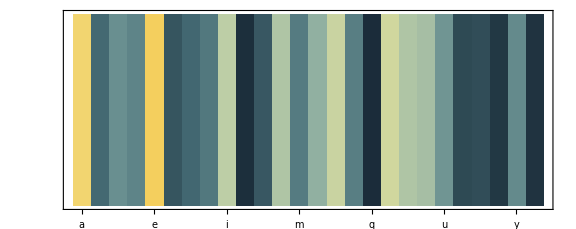

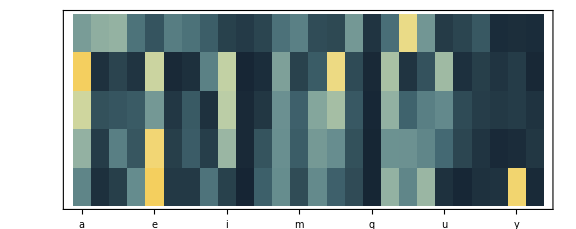

```mathematica
MatrixPlot[{ctl}/Max[ctl],FrameTicks->{None,Table[{i,Alphabet[][[i]]},{i,26}]},ImageSize->Large,ColorFunction->"StarryNightColors",ColorFunctionScaling->False]
MatrixPlot[(cil/Max[cil])^1,FrameTicks->{None,Table[{i,Alphabet[][[i]]},{i,26}]},ImageSize->Large,ColorFunction->"StarryNightColors",ColorFunctionScaling->False]
```

```mathematica
({{"m", "o", "u", "l", "d"}, {"c", "a", "r", "e", "t"}, {"s", "h", "i", "n", "y"}});
Print[%,", Green box - ",1.pts1[%],", Yellow box - ",1.pts2[%]]
```

(m | o | u | l | d
c | a | r | e | t
s | h | i | n | y), Green box - 2.76251, Yellow box - 1.41234